## Book Problems

### Chapter 6, Problem 3

```mathematica
DSolve[
{v''[x]+0 v[x]==0,
v'[0]+aL/(1+aL L) v[0]==0,
v'[L]+aL v[L]==0},
v[x],x]//FullSimplify//Expand
```

{{v[x]→-C[1]/aL-L C[1]+x C[1]}}

```mathematica
Reduce[{c1-a0 c2==0&&c1+aL c1 L+aL c2==0&&(c1!=0||c2!=0)}]//FullSimplify
```

a0==c1/c2&&aL+c1/(c2+c1 L)==0

```mathematica
tmp[x_]=C[1] Cos[x √λ]+C[2] Sin[x √λ];
tmp'[L]+aL tmp[x]//FullSimplify
```

aL C[1] Cos[x √λ]+√λ (C[2] Cos[L √λ]-C[1] Sin[L √λ])+aL C[2] Sin[x √λ]

### Chapter 6, Problem 8

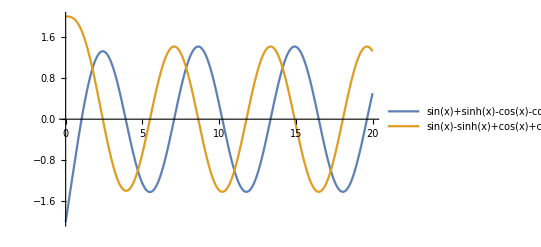

```mathematica
Plot[
{Sin[x]+Sinh[x]-Cos[x]-Cosh[x],
Sin[x]-Sinh[x]+Cos[x]+Cosh[x]
},{x,0,20},
PlotLegends->"Expressions"]
```

```mathematica
Assuming[λ>0&&L>0,
DSolve[
{v''''[x]-μ^4 v[x]==0,
v[0]==0,
v'[0]==0,
v''[L]==0,
v'''[L]==0},
v[x],x
]//FullSimplify]
v1[x_]=a Cos[μ x]+b Sin[μ x]+c Cosh[μ x]+d Sinh[μ x];
v1[0]//FullSimplify
v1'[0]//FullSimplify
v1''[L]/.{c->-a,d->-b}/.{b->-a}//FullSimplify
v1'''[L]/.{c->-a,d->-b}/.{b->-a}//FullSimplify
Reduce[Sin[x]+Sinh[x]-Cos[x]-Cosh[x]==0&&Sin[x]-Sinh[x]+Cos[x]+Cosh[x]==0]//FullSimplify
Assuming[μ!=0&&L>0,v1[0]==0&&v1'[0]==0&&v1''[L]==0&&v1'''[L]==0//FullSimplify]/.{c->-a,d->-b}//FullSimplify
```

{{v[x]→0}}

a+c

(b+d) μ

a μ^2 (-Cos[L μ]-Cosh[L μ]+Sin[L μ]+Sinh[L μ])

a μ^3 (Cos[L μ]+Cosh[L μ]+Sin[L μ]-Sinh[L μ])

Sin[x]==0&&Cos[x]+Cosh[x]==Sinh[x]

a Cos[L μ]+a Cosh[L μ]+b Sin[L μ]+b Sinh[L μ]==0&&b (Cos[L μ]+Cosh[L μ])+a Sinh[L μ]==a Sin[L μ]

```mathematica
FullSimplify[(-(Cos[L μ]+Cosh[L μ])^2+Sinh[L μ]^2-Sin[L μ]^2)/(Sin[L μ]+Sinh[L μ])==0]
```

(1+Cos[L μ] Cosh[L μ])/(Sin[L μ]+Sinh[L μ])==0

```mathematica
DSolve[
{v''[x]+λ v[x]==0},
v[x],x
]//FullSimplify
```

```mathematica
{{v[x]->C[1] Cos[x √λ]+C[2] Sin[x √λ]}}
```

```mathematica
v2[x_]=C[1] Cos[x √λ]+C[2] Sin[x √λ];
v2[0]
```

C[1]

## Additional Problems

### 1

### 2

### 3

### 4